{1.×10^-6,0.100001,0.200001,0.300001,0.400001,0.500001,0.600001,0.700001,0.800001,0.900001,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9}

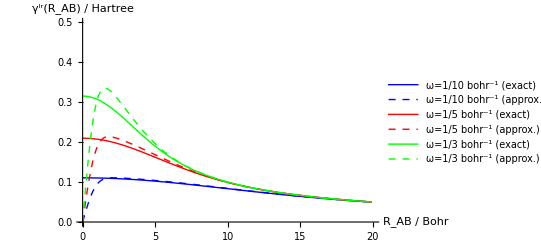

```mathematica
ω=0.1;
τA=2.0;
τB=2.0;
γABlrExact[ω_,x_]:=(2*τA^4*τB^4)/(π*x)*Quiet[NIntegrate[Sin[q*x]/(q*(q^2+τA^2)^2*(q^2+τB^2)^2)*Exp[-q^2/(4*ω^2)],{q,0,∞}]];
γABlrApprox[ω_,x_]:=1/x*Erf[ω*x]*Erf[x];
rs=Range[0.000001, 20.0, 0.1]
γABlrExactLine[ω_]:=Map[{#,γABlrExact[ω,#]}&,rs];
γABlrApproxLine[ω_]:=Map[{#,γABlrApprox[ω,#]}&,rs];
ListLinePlot[{
γABlrExactLine[0.1],γABlrApproxLine[0.1],
γABlrExactLine[0.2],γABlrApproxLine[0.2],
γABlrExactLine[1.0/3.0],γABlrApproxLine[1.0/3.0]
},
PlotRange->{{0,20},{0,0.5}}, 
PlotStyle->{Blue,{Dashed,Blue},Red,{Dashed,Red},Green,{Dashed,Green}},
AxesLabel->{"R_AB / Bohr", "γ^lr(R_AB) / Hartree"},
PlotLegends->{"ω=1/10 bohr^-1 (exact)","ω=1/10 bohr^-1 (approx.)","ω=1/5 bohr^-1 (exact)","ω=1/5 bohr^-1 (approx.)","ω=1/3 bohr^-1 (exact)","ω=1/3 bohr^-1 (approx.)"}]
Export["approx_0p1.dat", γABlrApproxLine[0.1]];
Export["approx_0p2.dat", γABlrApproxLine[0.2]];
Export["approx_0p333.dat", γABlrApproxLine[1.0/3.0]];
Export["exact_0p1.dat", γABlrExactLine[0.1]];
Export["exact_0p2.dat", γABlrExactLine[0.2]];
Export["exact_0p333.dat", γABlrExactLine[1.0/3.0]];
```